```mathematica
Exit[]
```

```mathematica
$Assumptions={_∈Reals, X0[x]∈Reals,Y0[x]∈Reals,aa>0,κ>0,β>0,Δ>0,lp>0,ϵ>0,λ[1]>0,λ[2]>0,λ[3]>0,Q1>0, μ>0,μ1>0,μ2>0,μ3>0,Δ>0,η>0,Px[x1]>0,Py[x1]>0,-3 K0[t]^2+Λ P0[t]<0,P0[t]>0,Sin[θ]>0};
```

## Ex[ z → -∞] vs Δ

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==40.3819,v2[3.×10^8]==20.4571}

## 循环

```mathematica
xM=3*10^8;
m=10;
mid=-350;
parameters={a-> 1,β->1,Rs->10^8,Δ->0.01m,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,mid,xM},Method->"ImplicitRungeKutta"]//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],v1[z]→InterpolatingFunction[…][z],v2[z]→InterpolatingFunction[…][z]}

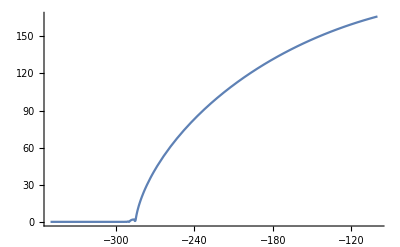

```mathematica
Plot[√(ⅇ^v1[z])/.nsolKv,{z,mid,-100},PlotRange->All]
```

```mathematica
newbdy={ K1[z1]->K1[z] , K2[z1]-> K2[z],Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]}/.nsolKv/.z-> mid/.z1-> mid
```

{K1[-350]→2.48365,K2[-350]→-1.85699,Ex[-350]→0.124823,Eϕ[-350]→9.68634×10^38}

```mathematica
bdyKu={K1[z]== K1[x0],K2[z]== K2[x0],u[z]==Log[Eϕ[x0]],Ex[z]== Ex[x0]}/.x0->mid/.newbdy/.z-> mid
```

{K1[-350]==2.48365,K2[-350]==-1.85699,u[-350]==89.769,Ex[-350]==0.124823}

```mathematica
neffeomODEKu={Table[eomKEuasym[[i]]==0,{i,1,3}],bdyKu}/.parameters//Flatten;
(*nsolutionODEKu1=NDSolve[neffeomODEKu,{K1[z],K2[z],Ex[z],u[z]},{z,-xM,-275},Method->"ImplicitRungeKutta"]//Flatten*)
KKEns=NDSolve[neffeomODEKu,{K1[z],K2[z],Ex[z]},{z,-xM,mid},Method-> {"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}]//Flatten;
uns=NDSolve[{(eomKEuasym[[4]]==0/.KKEns/.parameters),bdyKu},u[z],{z,-xM,mid},Method->"ImplicitRungeKutta"];
nsolutionODEKu={KKEns,uns}//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],Ex[z]→InterpolatingFunction[…][z],u[z]→InterpolatingFunction[…][z]}

```mathematica
dataEx[m]=√Ex[z]/.nsolutionODEKu/.z-> -xM
```

0.353302

```mathematica
asymEx=Table[dataEx[i],{i,1,m}]
```

{0.111724,0.158002,0.193512,0.223448,0.249823,0.273667,0.295594,0.316003,0.335172,0.353302}

```mathematica
eval[f_,x_]:=Module[{f1=((Simplify[f/.chvarearly/.D[chvarearly, z]]//Expand)/.nsolKv /.D[nsolKv, z]/.D[D[nsolKv, z], z]),f2=((Simplify[f/.chvar/.D[chvar, z]]//Expand)/.nsolutionODEKu /.D[nsolutionODEKu, z]/. D[D[nsolutionODEKu, z], z])},If[N[x]⩾mid,f1/.z->x,f2/.z->x]];
```

```mathematica
eval1[f_,x_]:=UnitStep[x-mid]*((Simplify[f/.chvarearly/.D[chvarearly, z]]//Expand)/.nsolKv /.D[nsolKv, z]/.D[D[nsolKv, z], z]/.z->x)+UnitStep[-(x-mid)]*((Simplify[f/.chvar/.D[chvar, z]]//Expand)/.nsolutionODEKu /.D[nsolutionODEKu, z]/. D[D[nsolutionODEKu, z], z]/.z->x);
```

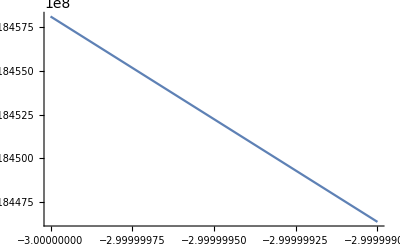

```mathematica
Λ=eval[Eϕ[z]/(√Ex[z]),y];
Plot[Log[Λ],{y,-xM,-xM+100},PlotRange->All]
```

```mathematica
model=LinearModelFit[Transpose[{Table[0.1i,{i,1,100}],Table[Log[Λ]/.y-> -xM+0.1i,{i,1,100}]}],x,x]
```

FittedModel[3.52185×10^8-1.17395 x]

```mathematica
lnΛ[z]=(Normal[model]/.x-> z+xM//Expand)
```

-300.575-1.17395 z

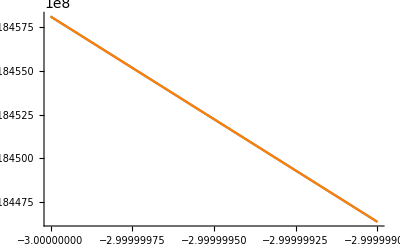

```mathematica
Show[Plot[Log[Λ],{y,-xM,-xM+100},PlotRange->All],Plot[lnΛ[z],{z,-xM,-xM+100},PlotRange->All,PlotStyle-> Orange]]
```

```mathematica
invradius[m]=√(L''[-t+x]/L[-t+x])/.{L[z_]-> ⅇ^lnΛ[z],L''[z_]-> D[D[ⅇ^lnΛ[z], z], z]}
```

1.17395

```mathematica
dsradius=Table[invradius[i]^-1,{i,1,m}]
```

{0.269371,0.380948,0.466564,0.538742,0.602331,0.659821,0.712688,0.761896,0.808112,0.851825}

```mathematica
(*Save[NotebookDirectory[]<>"asymEx and dsradius and parameters (Delta=0.01m, m=1--10).wl",{asymEx,dsradius,parameters}]*)
```

## 数据处理

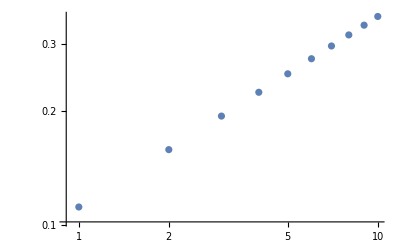

```mathematica
ListLogLogPlot[asymEx]
```

```mathematica
LinearModelFit[Transpose[{Log[Table[0.01m,{m,1,10}]],Log[asymEx]}],x,x]
```

FittedModel[0.110862+0.5 x]

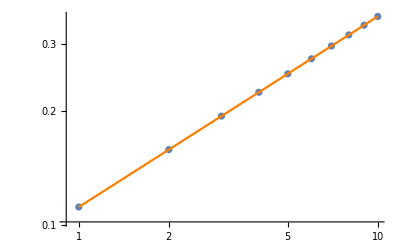

```mathematica
Show[ListLogLogPlot[asymEx],LogLogPlot[ⅇ^0.11086173017434924(0.01x)^(1/2),{x,1,10},PlotStyle->Orange]]
```

```mathematica
ⅇ^0.11086173017434924//N
```

1.11724

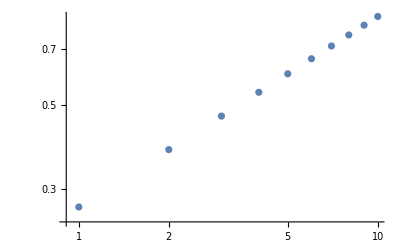

```mathematica
ListLogLogPlot[dsradius]
```

```mathematica
LinearModelFit[Transpose[{Log[Table[0.01m,{m,1,10}]],Log[dsradius]}],x,x]
```

FittedModel[0.990919+0.5 x]

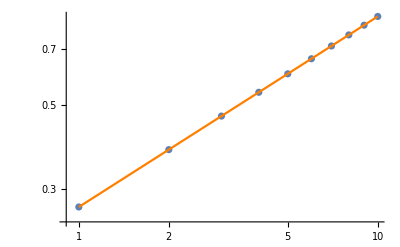

```mathematica
Show[ListLogLogPlot[dsradius],LogLogPlot[ⅇ^0.9909188006878559(0.01x)^(1/2),{x,1,10},PlotStyle->Orange]]
```

```mathematica
ⅇ^0.9909188006878559
```

2.69371

```mathematica
Kres=Kretschmann/.x-> t+z;
```

```mathematica
Kn=eval1[Kres,y];
Kn2=eval1[Kres/.Ex'[z]-> 0/.Ex''[z]-> 0,x];
```

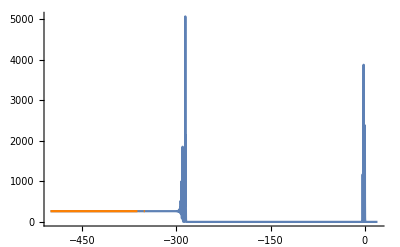

```mathematica
Show[Plot[Kn,{y,-500,20},PlotRange->All],Plot[Kn2,{x,-500,mid},PlotStyle-> Orange]]
```

```mathematica
eval1[Kres,-xM]
```

264.325

```mathematica
Kretschmanndss2/.{α-> dsradius[[m]],r0-> asymEx[[m]]}
```

264.325

## dS_2 × S^2

```mathematica
q={{-1,0,0,0},{0,ⅇ^(-2α1-2 α0^-1(x-t)),0,0},{0,0,r0^2,0},{0,0,0,r0^2 Sin[θ]^2}};
```

```mathematica
d=4;
xx={t,x,θ,ϕ};
```

```mathematica
qinv=FullSimplify[Inverse[q],Assumptions->{r0>0,α>0}]
```

{{-1,0,0,0},{0,ⅇ^((2 (-t+x+α0 α1))/α0),0,0},{0,0,1/r0^2,0},{0,0,0,Csc[θ]^2/r0^2}}

```mathematica
Christ = ParallelTable[Simplify[∑_(ρ=1)^d 1/2 qinv[[σ,ρ]](D[q[[ρ,μ]], xx[[ν]]]+D[q[[ρ,ν]], xx[[μ]]]-D[q[[μ,ν]], xx[[ρ]]]),Assumptions->{Rs>0}] , {σ, 1, d}, {μ, 1, d}, {ν, 1, d}];
```

```mathematica
Rie = ParallelTable[Simplify[-D[Christ[[σ,ν,ρ]], xx[[μ]]] + D[Christ[[σ,μ,ρ]], xx[[ν]]] + ∑_(λ=1)^d (Christ[[λ,ρ,μ]]Christ[[σ,ν,λ]]-Christ[[λ,ρ,ν]]Christ[[σ,μ,λ]]),Assumptions->{Rs>0}] , {μ, 1,d}, {ν, 1, d}, {ρ, 1, d}, {σ, 1, d}];
```

```mathematica
Ricci = ParallelTable[Simplify[∑_(ν=1)^d Rie[[μ,ν,ρ,ν]] ,Assumptions->{Rs>0}], {μ, 1, d}, {ρ, 1, d}];
RicciScalar = ∑_(a=1)^d ∑_(b=1)^d qinv[[a,b]]Ricci[[a,b]] ;
```

```mathematica
RicciScalar//Simplify
```

2 (1/r0^2+1/α0^2)

```mathematica
Kretschmanndss2=Simplify[∑_(a=1)^d ∑_(a1=1)^d ∑_(b=1)^d ∑_(b1=1)^d ∑_(c=1)^d ∑_(c1=1)^d ∑_(e=1)^d ∑_(e1=1)^d qinv[[a,a1]]qinv[[b,b1]]qinv[[c,c1]]q[[e,e1]]Rie[[a,b,c,e]]Rie[[a1,b1,c1,e1]],Assumptions->{r0>0,α>0}]
```

4 (1/r0^4+1/α0^4)

```mathematica
Ricci -1/α0^2 q
```

{{0,0,0,0},{0,-ⅇ^(-(2 (-t+x))/α0-2 α1)/α0^2+ⅇ^(-(2 (-t+x+α0 α1))/α0)/α0^2,0,0},{0,0,1-r0^2/α0^2,0},{0,0,0,Sin[θ]^2-(r0^2 Sin[θ]^2)/α0^2}}

```mathematica
4 (1/r0^4+1/α^4)/.{r0-> 1.1172404155364943 √Δ,α-> 2.6937083167445706 √Δ}
```

2.64325/Δ^2